Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Note: Mathematica has a section of commands dealing with graphs, but there seem to be some kinks in there. See problem 7.

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: Paclet[IGraphM,0.3.110,<>].

It can now be loaded using the command Get["IGraphM`"].

```mathematica
Get["IGraphM`"]
```

IGraph/M 0.3.110 (April 22, 2019)

Evaluate IGDocumentation[] to get started.

General comment. When I was putting the problem section together, I thought it was thorough. I made property lists of both EdgeCapacity and EdgeWeight, but find that I cannot always use them both.

1 - 6 Cut sets, capacity
Find T and cap (S, T) for:

1.  Figure 498, S = {1, 2, 4, 5}

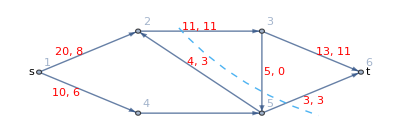

```mathematica
fig498=Graph[{1->2,2->3,3->6,4->5,5->6,1->4,5->2,3->5},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{20,11,13,7,3,10,4,5},EdgeWeight->{8,11,11,6,3,6,3,0},Epilog->{{Text[Style["s",Medium],{-2.15,-1}]},{Red,Text[Style["10, 6",Medium],{-1.45,-1.5}]},{Red,Text[Style["5, 0",Medium],{2.75,-1}]},{Red,Text[Style["20, 8",Medium],{-1.4,-0.5}]},{Red,Text[Style["3, 3",Medium],{3.55,-1.7}]},{Text[Style["t",Medium],{4.65,-1}]},{Red,Text[Style["4, 3",Medium],{1.2,-0.75}]},{Red,Text[Style["11, 11",Medium],{1.25,0.1}]},{Red,Text[Style["7, 6",Medium],{1.25,-2.15}]},{Red,Text[Style["13, 11",Medium],{3.95,-0.5}]},{Dashed,Thick,RGBColor[0.3,0.7,0.95],Circle[{6,4},6.5,{π+0.6,π+1.2}]},{Text[Style["Cut",Medium],{0.7,0.5}]}},ImageSize->400,ImagePadding->35]
```

A brief intuitive analysis will be enough. The problem description states which vertices will belong to the S region. The cut must come immediately downstream of these. So the downstream edges for analysis are 2->3 and 5->6. The capacity numbers for those two edges are 11, and 3, which add up to 14. The T region comprises those vertices which are not in the S region, here 3 and 6.

3.  Figure 498, S = {1, 2, 3}

By the problem description, The S region contains the vertices 1, 2, and 3. So the first downstream edges of the cut will be 1->4, 3->6, and 3->5. The edge 3->5 does not look like it is oriented exactly “downstream”, but it is not upstream, so it must be downstream. The T region comprises vertices 4, 5, and 6. The capacity numbers for these three edges are 10, 13 and 5, which sum to 28.

5.  Figure 499, S = {1, 2, 4, 5}

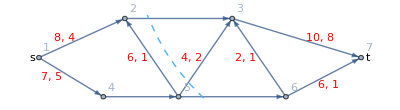

```mathematica
fig499=Graph[{1->2,2->3,6->3,4->5,5->6,1->4,5->2,5->3,3->7,6->7},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{3.75,-2},{-0.5,-2},{1.25,-2},{5.5,-1}},EdgeCapacity->{8,8,2,6,4,7,6,4,10,6},EdgeWeight->{4,5,2,5,2,5,1,2,8,1},Epilog->{{Text[Style["s",Medium],{-2.15,-1}]},{Red,Text[Style["7, 5",Medium],{-1.7,-1.5}]},{Red,Text[Style["2, 1",Medium],{2.8,-1}]},{Red,Text[Style["8, 4",Medium],{-1.4,-0.5}]},{Red,Text[Style["6, 1",Medium],{4.75,-1.7}]},{Text[Style["t",Medium],{5.65,-1}]},{Red,Text[Style["6, 1",Medium],{0.3,-1}]},{Red,Text[Style["8, 5",Medium],{1.25,0.15}]},{Red,Text[Style["6, 5",Medium],{0.3,-2.15}]},{Red,Text[Style["10, 8",Medium],{4.55,-0.5}]},{Red,Text[Style["4, 2",Medium],{1.55,-1}]},{Red,Text[Style["4, 2",Medium],{2.5,-2.15}]},Dashed,Thick,RGBColor[0.3,0.7,0.95],Circle[{6,2},5.8,{π,π+1.2}]},ImagePadding->15]
```

Now I will look at this one. The S region as given is 1, 2, 4, 5, which means the cut will cross 2->3, 5->3, and 5->6. The T region will have the vertices 3, 6, and 7. All of the cut edges are downstream edges. The total capacity in this case will be 16.

7 - 8 Minimum cut set
Find a minimum cut set and its capacity for the network:

7.  In figure 499.

```mathematica
Clear["Global`*"]
```

There are two places that make this choice a tie, and therefore weaken the problem. The text wants to cut 1->2 and 4->5, which is fine since it gives cap (S, T) of 14, the smallest available. But consider that allowing for 6->3 to be null due to direction, cutting 5->6 and 3->7 would also give 14. This is what the IGMinimumCut function below does. It makes the choice the text doesn’t. IGMC only responds to weighted edges though, so I have to call the EdgeCapacity by the name of EdgeWeight. Where did this IGMinimumCut function come from? It seems there are a number of serious bugs in Mathematica’s graph faculties, continuing through ver 11, and talked about at places like https://mathematica.stackexchange.com/questions/173936/s-t-min-cut-in-a-graph. That is where I got the add-ons referred to by the “Gets” at the top of the notebook. Author: Szabolcs. Looking at the below, I notice one interesting thing, which is that minimum edge cut functions do not need to know the coordinates of vertices in order to determine if they are upstream or downstream.

```mathematica
IGMinimumCut[Graph[{1->2,2->3,6->3,4->5,5->6,1->4,5->2,5->3,3->7,6->7},EdgeWeight->{8,8,2,6,4,7,6,4,10,6}],1,7]
```

{5->6,3->7}

```mathematica
IGMinimumCutValue[Graph[{1->2,2->3,6->3,4->5,5->6,1->4,5->2,5->3,3->7,6->7},EdgeWeight->{8,8,2,6,4,7,6,4,10,6}],1,7]
```

14.

9.  Why are backward edges not considered in the definition of the capacity of a cut set?

12 - 15 Flow augmenting paths
Find flow augmenting paths:

13.   Problem represented by a diagram.

```mathematica
Clear["Global`*"]
```

I start with a plot which resembles the associated figure in the text. However I feel now that the level of detail is more trouble to assemble than it is worth. As for augmenting paths, I looked for and did not find an algorithm. It seems the best one would be Dinic, next best Edmonds-Karp. If anyone has written Mathematica ports of these, they are not easy to find.

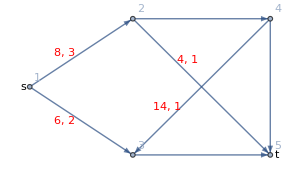

```mathematica
g13=Graph[{2->4,4->5,3->5,1->3,1->2,2->5,4->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{2,0},{2,-2},{0,-2},{-1.5,-1}},EdgeCapacity->{10,4,12,6,8,4,14},EdgeWeight->{2,2,3,2,3,1,1},Epilog->{{Text[Style["s",Medium],{-1.6,-1}]},{Red,Text[Style["6, 2",Medium],{-1,-1.5}]},{Red,Text[Style["4, 2",Medium],{2.2,-1}]},{Red,Text[Style["8, 3",Medium],{-1,-0.5}]},{Red,Text[Style["14, 1",Medium],{0.5,-1.3}]},{Text[Style["t",Medium],{2.1,-2}]},{Red,Text[Style["4, 1",Medium],{0.8,-0.6}]},{Red,Text[Style["10, 2",Medium],{1,0.1}]},{Red,Text[Style["12, 3",Medium],{1,-2.1}]}},ImageSize->300,ImagePadding->20]
```

I execute an IG command to double check the Mathematica command.

```mathematica
IGMaximumFlowValue[Graph[{2->4,4->5,3->5,1->3,1->2,2->5,4->3},VertexCoordinates->{{0,0},{2,0},{2,-2},{0,-2},{-1.5,-1}},EdgeCapacity->{10,4,12,6,8,4,14},EdgeWeight->{2,2,3,2,3,1,1}],1,5]
```

14.

I run the Mathematica command to find out the maximum flow. This is just a sum of the EdgeWeights, indicating, I guess, that under assumed ideal conditions that much flow would go through.

```mathematica
gdc=FindMaximumFlow[Graph[{2->4,4->5,3->5,1->3,1->2,2->5,4->3},EdgeCapacity->{10,4,12,6,8,4,14},EdgeWeight->{2,2,3,2,3,1,1}],1,5, "FlowValue"]
```

14

Then I run the command again, but this time I specify an EdgeList. Even though it is still a FindMaximum command, the edges that are delivered seem to be the ones that can be effective. One edge is dropped.

```mathematica
gdd=FindMaximumFlow[Graph[{2->4,4->5,3->5,1->3,1->2,2->5,4->3},EdgeCapacity->{10,4,12,6,8,4,14},EdgeWeight->{2,2,3,2,3,1,1}],1,5, "EdgeList"]
```

{2->4,2->5,4->5,3->5,1->3,1->2}

I back up and look at the difference between edge capacities and edge weights. These residuals are what are potential contributors to augmenting paths. But they will only be applicable for effective edges.

```mathematica
ec={10,4,12,6,8,4,14};
ew={2,2,3,2,3,1,1};
```

```mathematica
residuals=Flatten[Table[{ec[[n]]-ew[[n]]},{n,1,7}]]
```

{8,2,9,4,5,3,13}

I get a graph of the outcome, using the residuals on their own respective edges.

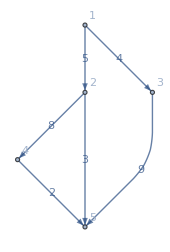

```mathematica
gdg=Graph[{Labeled[2->4,"8"],Labeled[2->5,"3"],Labeled[4->5,"2"],Labeled[3->5,"9"],Labeled[1->3,"4"],Labeled[1->2,"5"]},VertexLabels->"Name",ImageSize->170,ImagePadding->20]
```

The edge values and minimum path flows in the above graph match the answer in the text. The total of the three effective paths is 9, which, however, the text does not specifically state.

15.  Problem represented by a diagram.

I do this problem in the same way as the last, though without clarifying notes.

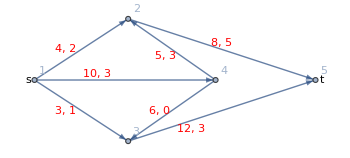

```mathematica
g15=Graph[{2->5,4->2,4->3,1->2,3->5,1->3,1->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{3,-1},{1.4,-1},{0,-2},{-1.5,-1}},EdgeCapacity->{8,5,6,4,1,3,10},EdgeWeight->{5,3,0,2,1,1,3},Epilog->{{Text[Style["s",Medium],{-1.6,-1}]},{Red,Text[Style["3, 1",Medium],{-1,-1.5}]},{Red,Text[Style["10, 3",Medium],{-0.5,-0.9}]},{Red,Text[Style["4, 2",Medium],{-1,-0.5}]},{Red,Text[Style["6, 0",Medium],{0.5,-1.5}]},{Text[Style["t",Medium],{3.1,-1}]},{Red,Text[Style["5, 3",Medium],{0.6,-0.6}]},{Red,Text[Style["8, 5",Medium],{1.5,-0.4}]},{Red,Text[Style["12, 3",Medium],{1,-1.8}]}},ImageSize->350,ImagePadding->20]
```

```mathematica
IGMaximumFlowValue[Graph[{2->5,4->2,4->3,1->2,3->5,1->3,1->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{3,-1},{1.4,-1},{0,-2},{-1.5,-1}},EdgeCapacity->{8,5,6,4,1,3,10},EdgeWeight->{5,3,0,2,1,1,3}],1,5]
```

9.

```mathematica
gdc15=FindMaximumFlow[Graph[{2->5,4->2,4->3,1->2,3->5,1->3,1->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{3,-1},{1.4,-1},{0,-2},{-1.5,-1}},EdgeCapacity->{8,5,6,4,1,3,10},EdgeWeight->{5,3,0,2,1,1,3}],1,5]
```

9

```mathematica
gdd15=FindMaximumFlow[Graph[{2->5,4->2,4->3,1->2,3->5,1->3,1->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{3,-1},{1.4,-1},{0,-2},{-1.5,-1}},EdgeCapacity->{8,5,6,4,1,3,10},EdgeWeight->{5,3,0,2,1,1,3}],1,5,"EdgeList"]
```

{2->5,4->2,3->5,1->2,1->3,1->4}

```mathematica
ec={8,5,6,4,1,3,10};
ew={5,3,0,2,1,1,3};
residuals=Flatten[Table[{ec[[n]]-ew[[n]]},{n,1,7}]]
```

{3,2,6,2,0,2,7}

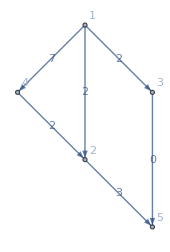

```mathematica
gdg15=Graph[{Labeled[2->5,"3"],Labeled[4->2,"2"],Labeled[3->5,"0"],Labeled[1->2,"2"],Labeled[1->3,"2"],Labeled[1->4,"7"]},VertexLabels->"Name",ImageSize->170,ImagePadding->20]
```

The edges values and minimum path flows in the above graph match the answer in the text (except the “etc.” in the text avoids listing the 0 flow path. The total of the two left side effective paths (upstream of vertex 2) is 4, which, however, is incompatible with the maximum allowed through 2->5, which is 3, so the answer must be 3. The total is something the text answer does not address.

16 - 19 Maximum flow
Find the maximum flow by inspection:

17.  Problem represented by a diagram.

```mathematica
Clear["Global`*"]
```

For these maximum flow problems, it is edge capacity that controls the flow. That is okay for Mathematica, because it knows how to use the EdgeCapacity property.

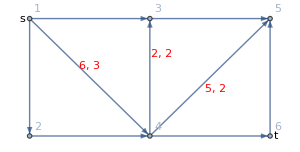

```mathematica
g17=Graph[{1->3,3->5,2->4,4->6,1->2,4->3,6->5,1->4,4->5},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-2,-2},{0,-2},{2,-2}},EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{5,7,2,1,2,2,9,3,2},Epilog->{{Text[Style["s",Medium],{-2.12,0}]},{Red,Text[Style["4, 2",Medium],{-1,-2.1}]},{Red,Text[Style["13, 9",Medium],{2.22,-1}]},{Red,Text[Style["6, 3",Medium],{-1,-0.8}]},{Red,Text[Style["5, 2",Medium],{1.1,-1.2}]},{Text[Style["t",Medium],{2.1,-2}]},{Red,Text[Style["2, 2",Medium],{0.2,-0.6}]},{Red,Text[Style["11, 7",Medium],{1,0.1}]},{Red,Text[Style["4, 1",Medium],{1,-2.1}]},{Red,Text[Style["8, 5",Medium],{-1,0.1}]},{Red,Text[Style["5, 2",Medium],{-2.2,-1}]}},ImageSize->300,ImagePadding->20]
```

```mathematica
gda17=Graph[{1->3,3->5,2->4,4->6,1->2,4->3,6->5,1->4,4->5},EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{5,7,2,1,2,2,9,3,2}];
```

Mathematica is set up for a fall on the next cell. Only three edges survive the culling. This is due to the yellow comment below.

```mathematica
gdc17=FindMaximumFlow[Graph[{1->3,3->5,2->4,4->6,1->2,4->3,6->5,1->4,4->5},EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{5,7,2,1,2,2,9,3,2}],1,6,"EdgeList"]
```

{1->2,2->4,4->6}

```mathematica
ec={8,11,4,4,5,2,13,6,5};
ew={5,7,2,1,2,2,9,3,2};
residuals=Flatten[Table[{ec[[n]]-ew[[n]]},{n,1,9}]]
```

{3,4,2,3,3,0,4,3,3}

```mathematica
gdc17=FindMaximumFlow[Graph[{1->3,3->5,2->4,4->6,1->2,4->3,6->5,1->4,4->5},EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{5,7,2,1,2,2,9,3,2}],1,6]
```

4

```mathematica
IGEdgeProp[EdgeCapacity][gda17]
```

{8,11,4,4,5,2,13,6,5}

```mathematica
IGMaximumFlowValue[Graph[{1->3,3->5,2->4,4->6,1->2,4->3,6->5,1->4,4->5},VertexLabels->"Name",EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{5,7,2,1,2,2,9,3,2}],1,6]
```

4.

```mathematica
IGMaximumFlowValue[gda17,1,6]
```

4.

The diagram that IG produces tells the tale. Only one pipe leads into vertex 6, and it has EdgeCapacity 4. So the max flow has to be 4.

```mathematica
IGMaximumFlow[Graph[{Labeled[1->3,"8"],Labeled[3->5,"11"],Labeled[2->4,"4"],Labeled[4->6,"4"],Labeled[1->2,"5"],Labeled[4->3,"2"],Labeled[6->5,"13"],Labeled[1->4,"6"],Labeled[4->5,"5"]},VertexLabels->"Name",EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{8,11,4,4,5,2,13,6,5},ImageSize->125],1,6]
```

IGMaximumFlow[-Graphics-,1,6]

```mathematica
flowMat=IGMaximumFlowMatrix[gda17,1,6]
```

SparseArray[<9>, {6, 6}]

```mathematica
MatrixForm[flowMat]
```

(0. | 0. | 0. | 4. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4. | 0.
0. | 0. | 0. | 0. | 0. | 4.
0. | 0. | 0. | 0. | 0. | 0.)

Taking account of the note below in yellow, the new flow in the following diagram is obviously changed to 17. And the only change to edges was Labeled[5->6,”13”] instead of Labeled[6->5,”13”].

```mathematica
IGMaximumFlow[Graph[{Labeled[1->3,"8"],Labeled[3->5,"11"],Labeled[2->4,"4"],Labeled[4->6,"4"],Labeled[1->2,"5"],Labeled[4->3,"2"],Labeled[5->6,"13"],Labeled[1->4,"6"],Labeled[4->5,"5"]},VertexLabels->"Name",EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{8,11,4,4,5,2,13,6,5},ImageSize->125],1,6]
```

IGMaximumFlow[-Graphics-,1,6]

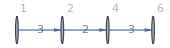

```mathematica
gdg17=Graph[{Labeled[1->2,"3"],Labeled[2->4,"2"],Labeled[4->6,"3"]},VertexLabels->"Name",ImageSize->170,ImagePadding->20]
```

The answer in the yellow cell above does not match the answer in the text. However, I think there is an error in the problem’s figure, or in the text answer. Consider the full text answer: “Subscript[f, 13]=f_35=8, f_14= f_45 =5, f_12 =f_24 = f_46 =4, f_56 =13, f=4+13 = 17, f = 17 is unique.” The subscript order in 6 of 7 cases of f_ij matches the arrowhead position in the figure. But in f_56 it is reversed. This is suspicious. So if I write

```mathematica
gdc17=FindMaximumFlow[Graph[{1->3,3->5,2->4,4->6,1->2,4->3,5->6,1->4,4->5},EdgeCapacity->{8,11,4,4,5,2,13,6,5},EdgeWeight->{5,7,2,1,2,2,9,3,2}],1,6]
```

17

with the edge 5->6 matching the text answer, I get the text answer.

19.  Problem represented by a diagram.

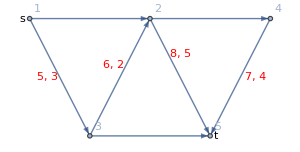

```mathematica
g19=Graph[{1->2,2->4,3->5,4->5,1->3,3->2,2->5},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-1,-2},{1,-2}},EdgeCapacity->{10,8,3,7,5,6,8},EdgeWeight->{7,4,1,4,3,2,5},Epilog->{{Text[Style["s",Medium],{-2.12,0}]},{Red,Text[Style["3, 1",Medium],{0,-2.15}]},{Red,Text[Style["7, 4",Medium],{1.75,-1}]},{Red,Text[Style["6, 2",Medium],{-0.6,-0.8}]},{Text[Style["t",Medium],{1.1,-2}]},{Red,Text[Style["8, 5",Medium],{0.5,-0.6}]},{Red,Text[Style["8, 4",Medium],{1,0.1}]},{Red,Text[Style["10, 7",Medium],{-1,0.1}]},{Red,Text[Style["5, 3",Medium],{-1.7,-1}]}},ImageSize->300,ImagePadding->20]
```

```mathematica
gdc19=FindMaximumFlow[Graph[{1->2,2->4,3->5,4->5,1->3,3->2,2->5},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-1,-2},{1,-2}},EdgeCapacity->{10,8,3,7,5,6,8},EdgeWeight->{7,4,1,4,3,2,5}],1,5]
```

15

The answer in the cell above matches the answer in the text. However, this was not done in the accepted way, so maybe I should expand.

```mathematica
gdc19=FindMaximumFlow[Graph[{1->2,2->4,3->5,4->5,1->3,3->2,2->5},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-1,-2},{1,-2}},EdgeCapacity->{10,8,3,7,5,6,8},EdgeWeight->{7,4,1,4,3,2,5}],1,5,"EdgeList"]
```

{1->2,1->3,2->4,2->5,4->5,3->5,3->2}

This gives me a hint. No edges were removed by the FMF command, so they must all be effective, hence the green cells stands. If I ask for OptimumFlowData I get contributing edges, vertices, and flow value.

```mathematica
gdc19=FindMaximumFlow[Graph[{1->2,2->4,3->5,4->5,1->3,3->2,2->5},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-1,-2},{1,-2}},EdgeCapacity->{10,8,3,7,5,6,8},EdgeWeight->{7,4,1,4,3,2,5}],1,5,"OptimumFlowData"]
```

OptimumFlowData[<5>, <7>]

I can try out the IG versions of these commands. (Treating now 2->5 and 3->2 as backward edges)

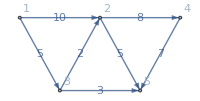
IGMaximumFlow[-Graphics-,1,5]

```mathematica
IGMaximumFlow[Graph[{Labeled[1->2,"10"],Labeled[2->4,"8"],Labeled[3->5,"3"],Labeled[4->5,"7"],Labeled[1->3,"5"],Labeled[3->2,"2"],Labeled[2->5,"5"]},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-1,-2},{1,-2}},EdgeCapacity->{10,8,3,7,5,6,8},EdgeWeight->{7,4,1,4,3,2,5},ImageSize->200],1,5]
```

The IG commands are not very helpful today. I can’t even get the flow number by using IGMaximumFlowValue.

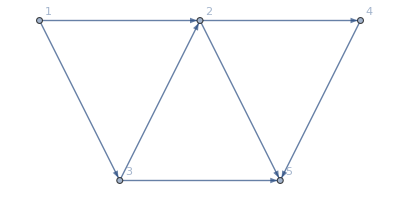
IGMaximumFlowValue[-Graphics-,1,5]

```mathematica
IGMaximumFlowValue[Graph[{1->2,2->4,3->5,4->5,1->3,3->2,2->5},VertexLabels->"Name",VertexCoordinates->{{-2,0},{0,0},{2,0},{-1,-2},{1,-2}},EdgeCapacity->{10,8,3,7,5,6,8},EdgeWeight->{7,4,1,4,3,2,5}],1,5]
```

This problem has me confused. I can’t claim that the text answer is wrong, because the text, Mathematica,  and IG agree that the max flow is 15. For both edges 3->2 and 2->5 the edge weight is used (reverse edge?), whereas 1->3 is a forward edge, based on the EdgeCapacity property being used. For now I have to think that what makes 2->5 a reverve edge is not its arrowhead, but the fact that it is split off at vertex 2. The text, p. 997, defines a backward edge as one directed from t to s. That appears not to be true in this case.